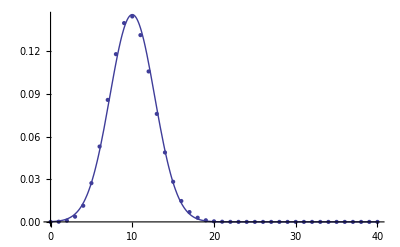
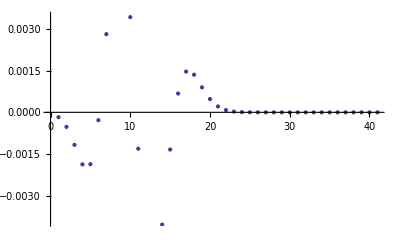

```mathematica
p[n_, k_, r_] = Binomial[n, k] r^k (1-r)^(n -k) ;
pApprox[n_, k_, r_] = 
Module[{s},s = 1 -r ;
(1/Sqrt[2 Pi n r s]) 
Exp[-(k - n r)^2/(2 n r s)] (* FIXME: had -n s in my notes ? *)
] ;
With[ {n = 40, r = 0.25}, 
Module[{t1, t2, p1, p2},
t1  = Table[{k,  p[n, k, r]}, {k, 0, n}] ;
t2  = Table[{k,  pApprox[n, k, r]}, {k, 0, n}] ;
p1 = ListPlot[t1, PlotRange -> Full] ;
p2 = Plot[ pApprox[n, k, r] , {k, 0, n}, PlotRange -> Full ] ;
Show[{p1, p2}]
]
ListPlot[Table[p[n, k, r] -pApprox[n, k, r], {k, 0, n}]] 
] (* with *)
```